Emaad Khwaja - Lagrange Interpolation - Math 385 - 03/28/16

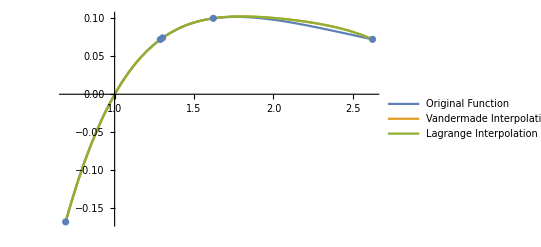

Norm Interpolation Error = 0.00177684

Norm Lagrange Interpolation Error = 0.00177684

The Lagrange Polynomial is the same as theVandermade Matrix Polynomial.

```mathematica
nb=EvaluationNotebook[];
NotebookFind[nb,"5",All,CellTags];

NumberofPoints= 5;
n1=NumberofPoints;
n=n1;
f[x_]:=x^(E^-x)-1
RandomPoints=RandomSample[DeleteCases[RandomReal[n,n],0],n];
V1=Partition[Riffle[RandomPoints,f[RandomPoints]],2];
V=V1;
A=IdentityMatrix[n]-IdentityMatrix[n];
b=RandomSample[Range[n],n];
xs=RandomSample[Range[n],n];
r=Range[(n)]-1;

For[i=0,i<n, i++
For[j=0,j<n,j++
If[i≥0,A[[j,i]]=V[[j,1]]^(i-1)]
]
];

If[Abs[Det[A]]>10^-6,
For[j=0,j<n, j++
If[j≥0,b[[j]]=V[[j,2]]]
];

For[j=0,j<n, j++
If[j≥0,xs[[j]]=V[[j,1]]]
];

a=N[LinearSolve[A,b]];

q=Sum[a[[i]]*(V[[i,1]]^r[[i]]),{i,1,n}];

g[x_]=Sum[a[[i]]*(x^r[[i]]),{i,1,n}];
u[x_]:=Evaluate[Sum[V[[j,2]]*Product[If[V[[i,1]]==V[[j,1]],1,(x-V[[i,1]])/(V[[j,1]]-V[[i,1]])],{i,1,5}],{j,1,5}]];

Show[Plot[{f[x],g[x],u[x]},{x,Min[xs],Max[xs]},PlotLegends->LineLegend[{"Original Function","Vandermade Interpolation","Lagrange Interpolation"}]],ListPlot[V]],SelectionEvaluate[nb]]

error1=1/(Max[xs]-Min[xs])*((NIntegrate[(f[x]-g[x])^2,{x,Min[xs],Max[xs]}])^(1/2));
error2=1/(Max[xs]-Min[xs])*((NIntegrate[(f[x]-u[x])^2,{x,Min[xs],Max[xs]}])^(1/2));

Print["Norm Interpolation Error = ", error1]
Print["Norm Lagrange Interpolation Error = ", error2]
Print["The Lagrange Polynomial is the same as theVandermade Matrix Polynomial."]
```